```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
nomicartelle=Import["/Users/pagani/mg5_3.5/lista_cartellemumumassive.dat","List"]
quantities={aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}
```

{aatottformuu,altottl,mupemtomupemtt,mupemtomupemtt_v0,mupemtomupemtt_v2,nocut_mupemtomupemtt,nocuts_altottl,onlyphoton_altottl,onlyphoton_mupemtomupemtt,onlyphoton_mupemtomupemtt_v0,onlyphoton_mupemtomupemtt_v2,onlyphoton_nocut_mupemtomupemtt,onlyphoton_nocuts_altottl}

{aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}

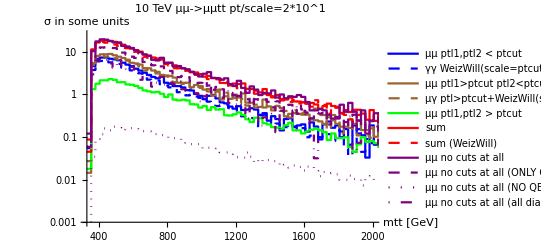

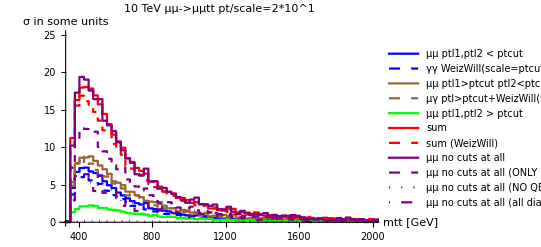

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf

```mathematica
namerun="distr2ndtry";
ptcutscale=ToString[1];


listaistogrammi=Table[0,{i,1,Length[nomicartelle]}];
Do[
nomi=.;
nhistos=.;
inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf";

If[i===6 || i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];

If[ i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];


Estrai[inputname,quantities[[i]],nomi,nhistos],
{i,1,Length[nomicartelle]}];


Estrai["/Users/pagani/mg5_3.5/"<>"mupemtottbar_nophotons"<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf",NPtotal,nomiNP,nhistosNP]
nomiNP=.;
nhistosNP=.;

numberplot=11;

unisci[x_]:=joinbin[x,5];

summed=sum[mumu[numberplot],sum[aa[numberplot],mua[numberplot]]];
summedWWa=sum[mumu[numberplot],sum[aaWW[numberplot],muaWW[numberplot]]];
ZPtotal=diff[total[numberplot],sum[NPtotal[numberplot],OPtotal[numberplot]]];

logplotmtt=ListLogPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[OPtotal[numberplot]],unisci[NPtotal[numberplot]],unisci[ZPtotal]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","μμ no cuts at all (ONLY QED)","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dashed},{Purple,Dotted},{Purple,DotDashed}},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

plotmtt=ListPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[OPtotal[numberplot]],unisci[NPtotal[numberplot]],unisci[ZPtotal]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","μμ no cuts at all (ONLY QED)","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dashed},{Purple,Dotted},{Purple,DotDashed}},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d"<>ToString[ptcutscale]<>".pdf",logplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d"<>ToString[ptcutscale]<>".pdf",plotmtt];

"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf"
"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf"
```

```mathematica
nomi
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_M},{14_DELTAR},{15_DELTAR},{16_DELTAR}}

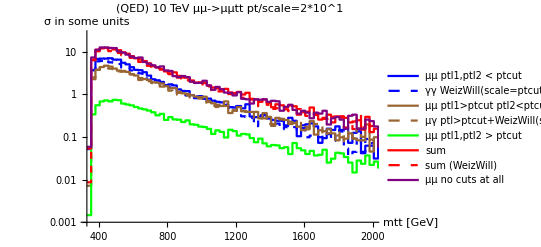

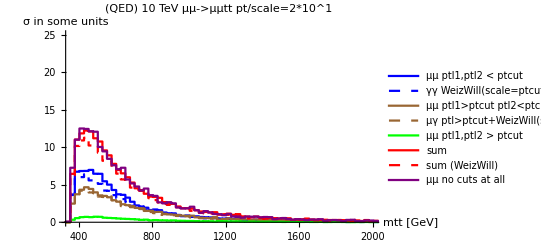

```mathematica
OPsummed=sum[OPmumu[numberplot],sum[OPaa[numberplot],OPmua[numberplot]]];
OPsummedWWa=sum[OPmumu[numberplot],sum[aaWW[numberplot],OPmuaWW[numberplot]]];
OPlogplotmtt=ListLogPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

OPplotmtt=ListPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPlogplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPlogplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPplotmtt];
```

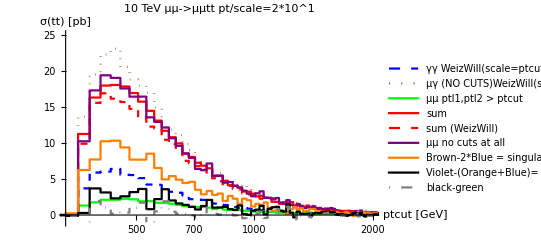

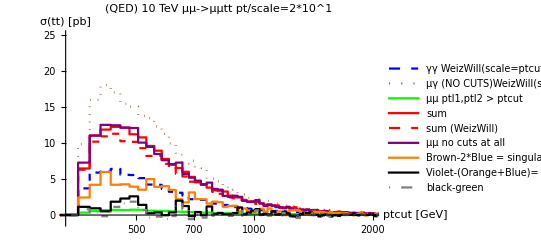

```mathematica
muaWWminus2aa=diff[nocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
nodiv=diff[total[numberplot],sum[aaWW[numberplot],muaWWminus2aa]];
OPmuaWWminus2aa=diff[OPnocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
OPnodiv=diff[OPtotal[numberplot],sum[aaWW[numberplot],OPmuaWWminus2aa]];


ListLogLinearPlot[{unisci[aaWW[numberplot]],unisci[nocutsmuaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[muaWWminus2aa],unisci[nodiv],unisci[diff[nodiv,mumu[numberplot]]]},Joined->True,InterpolationOrder->0,PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale],AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ WeizWill(scale=ptcut)","μγ (NO CUTS)WeizWill(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}},PlotRange->{{330,2000},{-1,25}}]

ListLogLinearPlot[{unisci[aaWW[numberplot]],unisci[OPnocutsmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]],unisci[OPmuaWWminus2aa],unisci[OPnodiv],unisci[diff[OPnodiv,OPmumu[numberplot]]]},Joined->True,InterpolationOrder->0,PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale],AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ WeizWill(scale=ptcut)","μγ (NO CUTS)WeizWill(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}},PlotRange->{{330,2000},{-1,25}}]
```

```mathematica
(*namerun="distr2ndtry";
ptcutscale=ToString[2];


listaistogrammi=Table[0,{i,1,Length[nomicartelle]}];
Do[
nomi=.;
nhistos=.;
inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf";

If[i===6 || i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];

If[ i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];


Estrai[inputname,quantities[[i]],nomi,nhistos],
{i,1,Length[nomicartelle]}]
numberplot=6;

unisci[x_]:=joinbin[x,5];

summed=sum[mumu[numberplot],sum[aa[numberplot],mua[numberplot]]];
summedWWa=sum[mumu[numberplot],sum[aaWW[numberplot],muaWW[numberplot]]];
logplotmtt=ListLogPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

plotmtt=ListPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]


"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf"
"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf"*)
```

```mathematica
(*OPsummed=sum[OPmumu[numberplot],sum[OPaa[numberplot],OPmua[numberplot]]];
OPsummedWWa=sum[OPmumu[numberplot],sum[aaWW[numberplot],OPmuaWW[numberplot]]];
OPlogplotmtt=ListLogPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

OPplotmtt=ListPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]*)
```

```mathematica
ZPtotal
```

{{-5.,0.},{0.,0.},{5.,0.},{10.,0.},{15.,0.},{20.,0.},{25.,0.},{30.,0.},{35.,0.},{40.,0.},{45.,0.},{50.,0.},{55.,0.},{60.,0.},{65.,0.},{70.,0.},{75.,0.},{80.,0.},{85.,0.},{90.,0.},{95.,0.},{100.,0.},{105.,0.},{110.,0.},{115.,0.},{120.,0.},{125.,0.},{130.,0.},{135.,0.},{140.,0.},{145.,0.},{150.,0.},{155.,0.},{160.,0.},{165.,0.},{170.,0.},{175.,0.},{180.,0.},{185.,0.},{190.,0.},{195.,0.},{200.,0.},{205.,0.},{210.,0.},{215.,0.},{220.,0.},{225.,0.},{230.,0.},{235.,0.},{240.,0.},{245.,0.},{250.,0.},{255.,0.},{260.,0.},{265.,0.},{270.,0.},{275.,0.},{280.,0.},{285.,0.},{290.,0.},{295.,0.},{300.,0.},{305.,0.},{310.,0.},{315.,0.},{320.,0.},{325.,0.},{330.,0.},{335.,0.},{340.,0.0605098},{345.,0.29059},{350.,0.4694},{355.,0.980515},{360.,0.408924},{365.,0.772897},{370.,0.864996},{375.,1.3885},{380.,1.94359},{385.,1.15625},{390.,0.815537},{395.,1.48712},{400.,1.40092},{405.,1.17259},{410.,1.08453},{415.,1.60674},{420.,1.24481},{425.,1.50147},{430.,1.05773},{435.,1.44148},{440.,1.1641},{445.,1.35161},{450.,0.711353},{455.,1.20563},{460.,0.951011},{465.,1.05404},{470.,1.2275},{475.,0.981807},{480.,0.269654},{485.,1.16314},{490.,0.524215},{495.,1.19755},{500.,1.27446},{505.,1.2677},{510.,1.52121},{515.,0.941489},{520.,0.742402},{525.,0.610084},{530.,0.416335},{535.,1.28927},{540.,0.854154},{545.,0.953772},{550.,0.389376},{555.,1.02037},{560.,0.915024},{565.,1.02643},{570.,0.740485},{575.,1.406},{580.,0.811717},{585.,0.619641},{590.,0.797931},{595.,0.614947},{600.,1.06869},{605.,0.597747},{610.,0.363169},{615.,0.774035},{620.,0.221618},{625.,0.608013},{630.,0.142966},{635.,0.607331},{640.,0.599862},{645.,0.0506068},{650.,0.996711},{655.,0.222706},{660.,0.851135},{665.,0.587468},{670.,0.552969},{675.,0.321891},{680.,0.790885},{685.,0.654217},{690.,0.292107},{695.,0.308723},{700.,-0.0666602},{705.,0.285523},{710.,0.500582},{715.,0.478499},{720.,0.301431},{725.,0.331383},{730.,0.572047},{735.,0.425879},{740.,0.231252},{745.,0.64377},{750.,0.93493},{755.,0.137719},{760.,0.239466},{765.,0.584805},{770.,0.495966},{775.,0.667119},{780.,0.130258},{785.,0.14516},{790.,0.247848},{795.,0.456578},{800.,0.390797},{805.,0.339851},{810.,0.750393},{815.,-0.076399},{820.,0.39103},{825.,0.762275},{830.,0.349947},{835.,0.0344062},{840.,0.195567},{845.,0.280542},{850.,0.431255},{855.,0.252044},{860.,0.320592},{865.,0.677553},{870.,0.0415093},{875.,0.335579},{880.,0.354662},{885.,0.337293},{890.,0.242369},{895.,0.396173},{900.,0.20839},{905.,0.154822},{910.,0.323592},{915.,0.12},{920.,0.391796},{925.,0.169191},{930.,0.42158},{935.,0.201392},{940.,0.152763},{945.,0.247941},{950.,0.0989424},{955.,0.262738},{960.,0.316131},{965.,0.130251},{970.,0.240395},{975.,0.281049},{980.,-0.0989234},{985.,-0.0842951},{990.,0.338987},{995.,-0.041245},{1000.,0.187522},{1005.,0.158251},{1010.,0.257096},{1015.,0.333261},{1020.,0.282335},{1025.,0.0267057},{1030.,0.53301},{1035.,0.306477},{1040.,0.481317},{1045.,0.531808},{1050.,0.235526},{1055.,0.172275},{1060.,-0.0153247},{1065.,0.173646},{1070.,0.320501},{1075.,0.236812},{1080.,0.365012},{1085.,-0.092684},{1090.,-0.000935321},{1095.,0.269252},{1100.,0.0350882},{1105.,0.284562},{1110.,0.185801},{1115.,0.0546846},{1120.,0.087469},{1125.,0.164231},{1130.,0.481142},{1135.,0.204969},{1140.,0.285848},{1145.,0.285932},{1150.,0.136421},{1155.,-0.0107789},{1160.,0.09791},{1165.,0.111162},{1170.,0.118279},{1175.,0.235266},{1180.,0.0530545},{1185.,0.0938772},{1190.,0.0788267},{1195.,0.228254},{1200.,0.375454},{1205.,0.176302},{1210.,0.107494},{1215.,0.0278163},{1220.,-0.041589},{1225.,0.216267},{1230.,0.0466399},{1235.,0.144888},{1240.,0.224565},{1245.,0.0954228},{1250.,-0.0153247},{1255.,0.0241277},{1260.,0.191268},{1265.,-0.0240514},{1270.,0.225422},{1275.,0.301671},{1280.,0.322898},{1285.,0.0456138},{1290.,-0.0114672},{1295.,0.186827},{1300.,0.176899},{1305.,0.0673531},{1310.,0.21541},{1315.,-0.147966},{1320.,-0.0226812},{1325.,0.0379976},{1330.,0.164744},{1335.,-0.0214798},{1340.,0.025329},{1345.,0.0979944},{1350.,0.134102},{1355.,0.0499842},{1360.,0.0578537},{1365.,-0.0526341},{1370.,-0.152252},{1375.,-0.0213953},{1380.,0.244506},{1385.,0.165257},{1390.,0.117162},{1395.,0.107663},{1400.,0.145745},{1405.,0.0880664},{1410.,0.215839},{1415.,-0.0621336},{1420.,-0.0102658},{1425.,0.103461},{1430.,0.0487829},{1435.,-0.0890861},{1440.,0.0760798},{1445.,0.265303},{1450.,0.067009},{1455.,0.128032},{1460.,0.0495556},{1465.,0.0454385},{1470.,0.0860923},{1475.,-0.0126686},{1480.,0.027472},{1485.,0.10852},{1490.,0.0674376},{1495.,0.157472},{1500.,0.178614},{1505.,-0.0425371},{1510.,-0.00016897},{1515.,0.017544},{1520.,0.18734},{1525.,0.0756512},{1530.,0.0387704},{1535.,0.156615},{1540.,-0.0428813},{1545.,0.147115},{1550.,0.225507},{1555.,-0.0209667},{1560.,0.24622},{1565.,-0.0130128},{1570.,0.205138},{1575.,-0.0196809},{1580.,0.0288424},{1585.,0.157985},{1590.,0.0678662},{1595.,0.115104},{1600.,0.0961047},{1605.,-0.018395},{1610.,0.00898636},{1615.,0.0644373},{1620.,-0.0520365},{1625.,-0.00479918},{1630.,0.117675},{1635.,-0.00308474},{1640.,0.0666648},{1645.,-0.0416799},{1650.,-0.0321805},{1655.,0.088664},{1660.,-0.00137029},{1665.,0.0181416},{1670.,-0.0208822},{1675.,-0.0112983},{1680.,-0.0606787},{1685.,-0.0395369},{1690.,0.217209},{1695.,0.0504974},{1700.,-0.130941},{1705.,-0.0234538},{1710.,0.07745},{1715.,0.0198561},{1720.,0.0567368},{1725.,0.017713},{1730.,-0.0100969},{1735.,0.0280696},{1740.,0.0268683},{1745.,0.0194274},{1750.,-0.0706912},{1755.,0.0068433},{1760.,0.0584512},{1765.,-0.0325247},{1770.,0.0280696},{1775.,-0.0017989},{1780.,0.0181416},{1785.,-0.0602501},{1790.,-0.0213108},{1795.,-0.0209667},{1800.,0.0484388},{1805.,0.0878912},{1810.,0.0692365},{1815.,0.11939},{1820.,-0.0611074},{1825.,0.108176},{1830.,0.0973905},{1835.,-0.00171445},{1840.,0.0795931},{1845.,0.0596526},{1850.,0.187853},{1855.,0.0474971},{1860.,0.0284983},{1865.,-0.0208822},{1870.,-0.0017989},{1875.,-0.0669182},{1880.,0.0372249},{1885.,0.0289269},{1890.,0.0488674},{1895.,-0.0507507},{1900.,0.0588798},{1905.,0.0679507},{1910.,0.00649914},{1915.,-0.0100125},{1920.,0.0580226},{1925.,-0.0295244},{1930.,0.0874626},{1935.,0.177925},{1940.,-0.0391082},{1945.,-0.0112983},{1950.,-0.0295244},{1955.,-0.00137029},{1960.,-0.0623932},{1965.,-0.0415955},{1970.,0.0662362},{1975.,0.00735636},{1980.,-0.0794179},{1985.,-0.00958386},{1990.,0.00949942},{1995.,0.0385107},{2000.,0.0388548},{2005.,-0.000857223},{2010.,0.108176},{2015.,-0.0117269},{2020.,0.0389393},{2025.,0.0973905},{2030.,0.0372249},{2035.,-0.00214306},{2040.,0.118188},{2045.,-0.0112983},{2050.,0.0376535},{2055.,0.0194274},{2060.,-0.0593929},{2065.,0.0580226},{2070.,-0.0191677},{2075.,0.0272969},{2080.,0.057594},{2085.,0.000772768},{2090.,-0.0195963},{2095.,-0.0203691},{2100.,0.0393679},{2105.,-0.0286672},{2110.,0.0593085},{2115.,0.0501532},{2120.,0.089177},{2125.,0.0385107},{2130.,-0.0598215},{2135.,-0.0203691},{2140.,0.0277255},{2145.,0.000772768},{2150.,-0.00257167},{2155.,0.0298685},{2160.,-0.000857223},{2165.,0.0306413},{2170.,-0.0394524},{2175.,0.0883198},{2180.,0.0402252},{2185.,0.147628},{2190.,0.0207133},{2195.,-0.039881},{2200.,-0.00171445},{2205.,0.00864219},{2210.,-0.00838248},{2215.,0.0584512},{2220.,0.00949942},{2225.,-0.0203691},{2230.,-0.0411668},{2235.,-0.0407382},{2240.,0.00821358},{2245.,0.0593085},{2250.,0.00907081},{2255.,-0.00128584},{2260.,-0.0606787},{2265.,-0.0207977},{2270.,-0.0187391},{2275.,-0.0290958},{2280.,-0.0403096},{2285.,0.0393679},{2290.,0.0294399},{2295.,0.00864219},{2300.,0.00949942},{2305.,0.00821358},{2310.,0.0393679},{2315.,0.0397966},{2320.,0.0670934},{2325.,0.00949942},{2330.,0.0281541},{2335.,0.00907081},{2340.,0.00949942},{2345.,-0.000428612},{2350.,0.},{2355.,-0.021655},{2360.,0.00907081},{2365.,0.0294399},{2370.,0.0103566},{2375.,0.0692365},{2380.,0.0393679},{2385.,-0.0104411},{2390.,0.0385107},{2395.,-0.00171445},{2400.,-0.0290958},{2405.,-0.0793334},{2410.,0.0688079},{2415.,0.00949942},{2420.,0.},{2425.,0.00864219},{2430.,0.00949942},{2435.,-0.00128584},{2440.,0.},{2445.,0.0290113},{2450.,0.0290113},{2455.,0.0103566},{2460.,-0.00128584},{2465.,0.0285827},{2470.,0.0588798},{2475.,0.00949942},{2480.,0.0883198},{2485.,0.00907081},{2490.,0.00907081},{2495.,-0.0104411},{2500.,-0.0390238},{2505.,0.0393679},{2510.,0.0593085},{2515.,0.0497246},{2520.,0.0584512},{2525.,-0.000857223},{2530.,0.0389393},{2535.,-0.0290958},{2540.,0.00949942},{2545.,0.00907081},{2550.,-0.00128584},{2555.,-0.0199405},{2560.,-0.00171445},{2565.,-0.039881},{2570.,-0.0394524},{2575.,-0.0199405},{2580.,0.0202847},{2585.,0.0285827},{2590.,0.0584512},{2595.,-0.00958386},{2600.,-0.0199405},{2605.,0.0285827},{2610.,-0.0195119},{2615.,0.0696651},{2620.,0.},{2625.,-0.0390238},{2630.,0.0281541},{2635.,-0.0203691},{2640.,-0.0207977},{2645.,-0.0403096},{2650.,0.0298685},{2655.,0.},{2660.,-0.000428612},{2665.,-0.0203691},{2670.,0.0294399},{2675.,-0.00171445},{2680.,0.0294399},{2685.,-0.0394524},{2690.,0.0402252},{2695.,-0.0199405},{2700.,-0.000428612},{2705.,-0.000428612},{2710.,-0.000857223},{2715.,-0.0195119},{2720.,-0.039881},{2725.,-0.0203691},{2730.,-0.000857223},{2735.,0.0294399},{2740.,-0.0203691},{2745.,0.},{2750.,-0.000857223},{2755.,0.0389393},{2760.,0.0588798},{2765.,0.},{2770.,0.00949942},{2775.,-0.00958386},{2780.,0.0393679},{2785.,0.0294399},{2790.,0.00949942},{2795.,0.0294399},{2800.,-0.0203691},{2805.,0.},{2810.,-0.0195119},{2815.,0.0294399},{2820.,0.0202847},{2825.,-0.000428612},{2830.,-0.000428612},{2835.,-0.00128584},{2840.,-0.000857223},{2845.,-0.0394524},{2850.,0.0103566},{2855.,-0.0203691},{2860.,0.0290113},{2865.,-0.000428612},{2870.,-0.000428612},{2875.,0.},{2880.,-0.000857223},{2885.,0.},{2890.,0.},{2895.,-0.0207977},{2900.,-0.0203691},{2905.,0.0298685},{2910.,-0.00128584},{2915.,-0.000857223},{2920.,-0.0394524},{2925.,-0.0195119},{2930.,-0.0195119},{2935.,-0.000428612},{2940.,-0.0195119},{2945.,-0.000857223},{2950.,-0.000428612},{2955.,0.0700937},{2960.,0.0294399},{2965.,0.0393679},{2970.,0.},{2975.,-0.000857223},{2980.,0.0103566},{2985.,0.00949942},{2990.,-0.000428612},{2995.,-0.0199405},{3000.,-0.0199405},{3005.,0.},{3010.,-0.0195119},{3015.,0.0294399},{3020.,-0.0195119},{3025.,0.0298685},{3030.,-0.0199405},{3035.,-0.000428612},{3040.,0.},{3045.,0.},{3050.,0.0298685},{3055.,-0.0199405},{3060.,-0.000428612},{3065.,-0.000428612},{3070.,0.00992803},{3075.,-0.0195119},{3080.,0.0294399},{3085.,-0.000428612},{3090.,0.},{3095.,0.},{3100.,-0.000428612},{3105.,-0.039881},{3110.,0.},{3115.,-0.0195119},{3120.,0.},{3125.,-0.000428612},{3130.,0.0290113},{3135.,0.0298685},{3140.,-0.000428612},{3145.,0.},{3150.,-0.0195119},{3155.,-0.0199405},{3160.,-0.00128584},{3165.,-0.00958386},{3170.,0.0294399},{3175.,0.},{3180.,0.0597371},{3185.,0.00992803},{3190.,-0.0390238},{3195.,-0.000428612},{3200.,-0.000428612},{3205.,-0.0195119},{3210.,0.},{3215.,-0.0199405},{3220.,0.0298685},{3225.,-0.000857223},{3230.,0.},{3235.,0.},{3240.,-0.000428612},{3245.,0.},{3250.,-0.0195119},{3255.,-0.000428612},{3260.,0.},{3265.,0.},{3270.,0.},{3275.,0.0298685},{3280.,-0.0195119},{3285.,-0.0195119},{3290.,-0.000428612},{3295.,0.},{3300.,0.},{3305.,0.0593085},{3310.,0.0298685},{3315.,-0.000428612},{3320.,0.0294399},{3325.,-0.000428612},{3330.,0.0298685},{3335.,0.0298685},{3340.,0.0294399},{3345.,0.00949942},{3350.,0.},{3355.,0.},{3360.,-0.0203691},{3365.,0.0593085},{3370.,-0.000428612},{3375.,-0.000857223},{3380.,-0.000428612},{3385.,-0.000428612},{3390.,0.},{3395.,-0.0195119},{3400.,-0.0195119},{3405.,0.},{3410.,0.},{3415.,-0.000428612},{3420.,0.0294399},{3425.,-0.00128584},{3430.,0.},{3435.,0.0294399},{3440.,0.},{3445.,0.},{3450.,0.},{3455.,-0.0195119},{3460.,-0.0195119},{3465.,-0.000428612},{3470.,-0.000857223},{3475.,-0.0195119},{3480.,-0.000428612},{3485.,0.0290113},{3490.,-0.0199405},{3495.,-0.000428612},{3500.,-0.000428612},{3505.,-0.000857223},{3510.,-0.00128584},{3515.,0.0294399},{3520.,0.},{3525.,-0.000428612},{3530.,0.},{3535.,0.},{3540.,0.},{3545.,0.0298685},{3550.,-0.0195119},{3555.,-0.000857223},{3560.,-0.000428612},{3565.,0.0298685},{3570.,-0.000857223},{3575.,-0.000428612},{3580.,-0.000428612},{3585.,-0.0199405},{3590.,0.},{3595.,0.},{3600.,0.0298685},{3605.,0.},{3610.,0.},{3615.,0.0298685},{3620.,0.},{3625.,0.},{3630.,-0.000428612},{3635.,-0.0195119},{3640.,-0.000428612},{3645.,-0.000857223},{3650.,0.},{3655.,0.},{3660.,0.0298685},{3665.,-0.0207977},{3670.,0.},{3675.,0.0298685},{3680.,-0.000428612},{3685.,-0.000428612},{3690.,0.},{3695.,-0.000428612},{3700.,0.0298685},{3705.,0.0298685},{3710.,0.},{3715.,-0.000428612},{3720.,0.},{3725.,0.},{3730.,0.},{3735.,0.},{3740.,0.},{3745.,0.},{3750.,-0.000428612},{3755.,0.},{3760.,-0.000857223},{3765.,0.},{3770.,-0.000428612},{3775.,0.},{3780.,-0.0195119},{3785.,-0.000857223},{3790.,0.},{3795.,0.},{3800.,-0.0195119},{3805.,0.},{3810.,0.},{3815.,0.0294399},{3820.,0.},{3825.,0.},{3830.,0.0298685},{3835.,0.0290113},{3840.,0.0298685},{3845.,-0.000857223},{3850.,-0.0195119},{3855.,0.},{3860.,0.0298685},{3865.,-0.0390238},{3870.,0.},{3875.,0.},{3880.,0.},{3885.,0.},{3890.,0.},{3895.,0.},{3900.,-0.0390238},{3905.,-0.000857223},{3910.,-0.0199405},{3915.,0.},{3920.,0.},{3925.,-0.0195119},{3930.,0.},{3935.,-0.000428612},{3940.,0.},{3945.,0.},{3950.,0.},{3955.,-0.0199405},{3960.,0.},{3965.,0.0103566},{3970.,0.0298685},{3975.,0.},{3980.,0.00992803},{3985.,0.},{3990.,0.0298685},{3995.,-0.000428612},{4000.,0.},{4005.,0.},{4010.,-0.000428612},{4015.,-0.0203691},{4020.,0.},{4025.,-0.000428612},{4030.,0.0103566},{4035.,-0.000428612},{4040.,-0.0195119},{4045.,-0.0199405},{4050.,-0.000428612},{4055.,0.},{4060.,0.},{4065.,0.},{4070.,-0.000428612},{4075.,0.0298685},{4080.,-0.000428612},{4085.,-0.0195119},{4090.,0.},{4095.,0.},{4100.,0.},{4105.,0.0294399},{4110.,0.},{4115.,-0.000428612},{4120.,-0.000428612},{4125.,0.},{4130.,0.},{4135.,-0.0199405},{4140.,0.0294399},{4145.,0.},{4150.,-0.0195119},{4155.,0.},{4160.,0.0298685},{4165.,0.0298685},{4170.,0.},{4175.,-0.000428612},{4180.,0.},{4185.,0.},{4190.,0.0298685},{4195.,0.},{4200.,0.},{4205.,-0.000428612},{4210.,-0.000428612},{4215.,0.},{4220.,0.},{4225.,0.},{4230.,0.},{4235.,0.},{4240.,0.},{4245.,0.},{4250.,0.},{4255.,0.},{4260.,0.},{4265.,0.},{4270.,0.},{4275.,-0.0195119},{4280.,-0.000428612},{4285.,0.},{4290.,0.},{4295.,0.},{4300.,0.},{4305.,0.},{4310.,0.},{4315.,-0.000428612},{4320.,0.},{4325.,0.0298685},{4330.,0.},{4335.,0.},{4340.,0.},{4345.,-0.0195119},{4350.,0.},{4355.,0.},{4360.,0.},{4365.,0.},{4370.,0.},{4375.,0.},{4380.,-0.000428612},{4385.,-0.000428612},{4390.,0.},{4395.,0.},{4400.,0.},{4405.,-0.000428612},{4410.,0.},{4415.,0.},{4420.,0.},{4425.,0.},{4430.,0.},{4435.,0.},{4440.,-0.0195119},{4445.,0.},{4450.,0.},{4455.,-0.0195119},{4460.,-0.000857223},{4465.,0.},{4470.,0.},{4475.,0.},{4480.,0.},{4485.,0.0298685},{4490.,0.},{4495.,-0.000428612},{4500.,0.},{4505.,-0.000428612},{4510.,0.},{4515.,0.0298685},{4520.,0.},{4525.,0.},{4530.,-0.000428612},{4535.,0.},{4540.,-0.000428612},{4545.,0.},{4550.,0.},{4555.,0.},{4560.,0.},{4565.,0.},{4570.,-0.000428612},{4575.,-0.000428612},{4580.,0.0298685},{4585.,0.},{4590.,0.},{4595.,0.},{4600.,-0.000428612},{4605.,-0.000428612},{4610.,0.},{4615.,0.},{4620.,0.},{4625.,0.},{4630.,0.0298685},{4635.,0.},{4640.,0.},{4645.,0.},{4650.,0.},{4655.,0.},{4660.,-0.0195119},{4665.,-0.000428612},{4670.,0.},{4675.,0.},{4680.,0.},{4685.,0.},{4690.,0.},{4695.,0.},{4700.,0.},{4705.,0.},{4710.,0.},{4715.,0.},{4720.,0.},{4725.,0.},{4730.,0.},{4735.,0.},{4740.,0.},{4745.,0.},{4750.,-0.000857223},{4755.,0.},{4760.,0.0294399},{4765.,-0.000857223},{4770.,0.},{4775.,0.},{4780.,-0.000428612},{4785.,0.},{4790.,-0.000428612},{4795.,0.},{4800.,0.},{4805.,0.},{4810.,0.},{4815.,-0.000428612},{4820.,0.},{4825.,0.},{4830.,0.},{4835.,0.},{4840.,0.},{4845.,0.},{4850.,-0.000428612},{4855.,0.},{4860.,0.},{4865.,0.},{4870.,-0.000428612},{4875.,0.},{4880.,0.},{4885.,0.},{4890.,0.},{4895.,0.},{4900.,-0.000428612},{4905.,0.},{4910.,0.},{4915.,0.},{4920.,0.},{4925.,0.},{4930.,0.},{4935.,0.},{4940.,0.},{4945.,0.},{4950.,0.},{4955.,0.},{4960.,0.},{4965.,0.},{4970.,0.},{4975.,0.},{4980.,0.},{4985.,-0.0195119},{4990.,0.},{4995.,0.},{5000.,0.14266}}